# The Simplest Set Replace Rules

Maksim Piskunov

## Prerequisites

We will be using SetReplace package for this essay.

```mathematica
If[PacletInformation["SetReplace"] === {} &&
		ChoiceDialog["SetReplace paclet needs to be installed. Proceed?"],
	PacletInstall[
		"https://github.com/maxitg/SetReplace/releases/download/0.1/SetReplace-0.1.paclet"]];
<< SetReplace`;
```

## Introduction

### Set Replace

Set Replace is a system that matches an unordered subset of expressions with a pattern, and replaces it with another subset. For example, consider a system that takes lists of 1 and 2 elements, joins them, and adding -1 at the end:

```mathematica
SetReplace[{{1},{4,5},{3},{6},{1,6},{3,4},{8,9},{10}},{{a_},{b_,c_}}:>{{a,b,c,-1}},4]
```

{{1,4,5,-1},{3,1,6,-1},{6,3,4,-1},{10,8,9,-1}}

Here we will only consider rules in which all elements are anonymous, that is, rules that never reference any elements explicitly. We can use a special syntax for that, for example, consider the same as the above, but without the -1 at the end.

```mathematica
output12to3=SetReplace[{{1},{4,5},{3},{6},{1,6},{3,4},{8,9},{10}},FromAnonymousRules[{{1},{2,3}}->{{1,2,3}}],4]
```

{{1,4,5},{3,1,6},{6,3,4},{10,8,9}}

One can also think of these systems are directed hypergraph substitution systems, where each list of the set represents an edge. For instance, we can plot the output above, coloring each edge in a different color

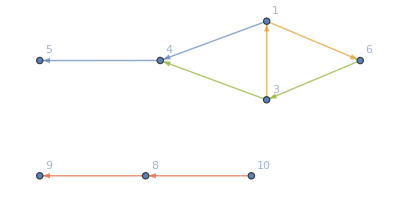

```mathematica
HypergraphPlot[output12to3,VertexLabels->"Name"]
```

If we specify vertices in the rule output that do not appear in its input, they will be created and assigned a unique name. For instance, consider the following rule, where 3 is a newly created vertex

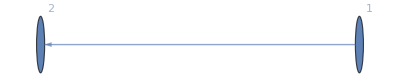
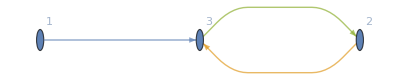
-Graphics-→-Graphics-

```mathematica
(rule[1]=({{1,2}}->{{1,3},{2,3},{3,2}}))//
```

After a few steps, we get newly created vertices

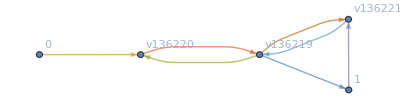

```mathematica
(SetReplace[init[1]={{0,1}},FromAnonymousRules[rule[1]],3])//
```

After more steps, we get

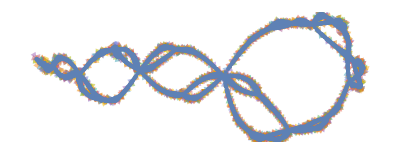

```mathematica
SetReplace[init[1],FromAnonymousRules[rule[1]],4000]//
```

Here is another example

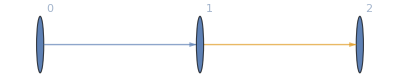
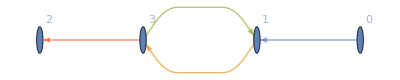
-Graphics-→-Graphics-

```mathematica
(rule[2]={{0,1},{1,2}}->{{0,1},{1,3},{3,1},{3,2}})//
```

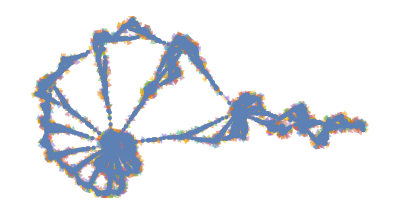

```mathematica
SetReplace[init[2]={{0,1},{1,2}},FromAnonymousRules[rule[2]],4000]//
```

And yet another example

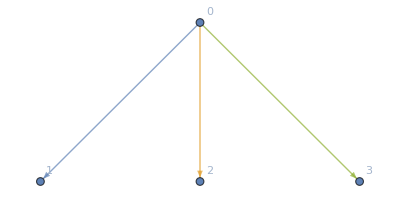
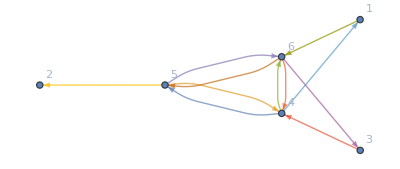
-Graphics-→-Graphics-

```mathematica
(rule[3]={{0,1},{0,2},{0,3}}->{{4,5},{5,4},{4,6},{6,4},{5,6},{6,5},{4,1},{5,2},{6,3},{1,6},{3,4}})//
```

```mathematica
SetReplace[init[3]={{0,0},{0,0},{0,0}},FromAnonymousRules[rule[3]],4000]//
```

-Graphics-

### Enumeration

The systems considered above are fairly large. They contain

```mathematica
Length@Flatten[{init[#],rule[#]}/.Rule->List]&/@Range[3]
```

{10,16,34}

vertices respectively (no unique vertices, but essentially all edges concatenated), including both the rule and the initial condition.

It is interesting, however, to consider the shortest possible systems, and see what classes of behaviour they can produce.

## Enumeration code

The idea is that we will consider all sequences of numbers (which will represents the vertices) of a given size, and then we will split each sequence into the initial condition and one or multiple rules.

The first task is to enumerate all sequences of vertices up to a given size. Consider the following code:

```mathematica
tuples[min_, 0] := {{}}
tuples[min_, count_] := tuples[min, count] =
	Flatten[Table[Join[{k}, #] & /@ tuples[Max[k + 1, min], count - 1], {k, 1, min}], 1]
tuples[count_] := tuples[1, count]
```

That does not enumerate all sequences, but only the ones for which every prefix contains all integers in Range[n] for some n.

It works by recursing into suffixes after selecting the integer in a given suffix which is no larger than the integers that came before. So, for example

```mathematica
tuples[4]
```

{{1,1,1,1},{1,1,1,2},{1,1,2,1},{1,1,2,2},{1,1,2,3},{1,2,1,1},{1,2,1,2},{1,2,1,3},{1,2,2,1},{1,2,2,2},{1,2,2,3},{1,2,3,1},{1,2,3,2},{1,2,3,3},{1,2,3,4}}

Next, we will need to partition these lists of numbers into edges. This is done by inserting list brakes between neighboring numbers in all possible ways (which are 2^(n-1))

```mathematica
allPartitions[s_] := ((SplitBy[#, # == -1 &] /. {0 -> Nothing, {-1} -> Nothing} &)
	/@ (Riffle[s, #] &)
	/@ Table[-IntegerDigits[k, 2, Length[s] - 1], {k, 0, 2^(Length[s] - 1) - 1}])
```

For instance,

```mathematica
allPartitions[{1,2,3,4}]
```

{{{1,2,3,4}},{{1,2,3},{4}},{{1,2},{3,4}},{{1,2},{3},{4}},{{1},{2,3,4}},{{1},{2,3},{4}},{{1},{2},{3,4}},{{1},{2},{3},{4}}}

Finally, we will need to split the rules into input edges and output edges

```mathematica
partitionsInTwo[s_] := Table[{s[[1 ;; k]], s[[k + 1 ;; Length[s]]]}, {k, 1, Length[s] - 1}]
```

```mathematica
partitionsInTwo[{1,2,3,4}]
```

{{{1},{2,3,4}},{{1,2},{3,4}},{{1,2,3},{4}}}

Now we have all the pieces, we can produce all rules up to a given size. We don’t care about the order of output edges, so we deduplicate them

```mathematica
allRules[n_] := allRules[n] = (Union
	@ (Map[Sort, #, {2}] &)
	@ (Rule
		@@@ (Flatten[#, 1] &)
		@ (partitionsInTwo
			/@ (Flatten[#, 1] &)
			@ (allPartitions
				/@ tuples[n]))))
```

```mathematica
allRules[3]
```

{{{1}}→{{1,1}},{{1}}→{{1,2}},{{1}}→{{2,1}},{{1}}→{{2,2}},{{1}}→{{2,3}},{{1}}→{{1},{1}},{{1}}→{{1},{2}},{{1}}→{{2},{2}},{{1}}→{{2},{3}},{{1,1}}→{{1}},{{1,1}}→{{2}},{{1,2}}→{{1}},{{1,2}}→{{2}},{{1,2}}→{{3}},{{1},{1}}→{{1}},{{1},{1}}→{{2}},{{1},{2}}→{{1}},{{1},{2}}→{{2}},{{1},{2}}→{{3}}}

Next we can produce all possible multiple rule sets by enumerating all possible partitions of rule sizes, and then removing rules with identical inputs, and finally deduplicating identical (but differently ordered) rule sets.

```mathematica
allMultirules[0] := {}
allMultirules[n_] := allMultirules[n] = Union[
	Sort
		/@ Select[DuplicateFreeQ[#⟦All, 1⟧] &]
		@ Flatten[Tuples /@ Map[allRules, IntegerPartitions[n], {2}], 1]]
```

As an example, here are all pairs of rules of total size 5

```mathematica
Select[Length[#]==2&]@allMultirules[5]
```

{{{{1}}→{{1}},{{1,1}}→{{1}}},{{{1}}→{{1}},{{1,1}}→{{2}}},{{{1}}→{{1}},{{1,2}}→{{1}}},{{{1}}→{{1}},{{1,2}}→{{2}}},{{{1}}→{{1}},{{1,2}}→{{3}}},{{{1}}→{{1}},{{1},{1}}→{{1}}},{{{1}}→{{1}},{{1},{1}}→{{2}}},{{{1}}→{{1}},{{1},{2}}→{{1}}},{{{1}}→{{1}},{{1},{2}}→{{2}}},{{{1}}→{{1}},{{1},{2}}→{{3}}},{{{1}}→{{2}},{{1,1}}→{{1}}},{{{1}}→{{2}},{{1,1}}→{{2}}},{{{1}}→{{2}},{{1,2}}→{{1}}},{{{1}}→{{2}},{{1,2}}→{{2}}},{{{1}}→{{2}},{{1,2}}→{{3}}},{{{1}}→{{2}},{{1},{1}}→{{1}}},{{{1}}→{{2}},{{1},{1}}→{{2}}},{{{1}}→{{2}},{{1},{2}}→{{1}}},{{{1}}→{{2}},{{1},{2}}→{{2}}},{{{1}}→{{2}},{{1},{2}}→{{3}}}}

For initial conditions, we will need to enumerate all graphs. This requires different code because we don’t care about the order of edges here, whereas we did care about it while generating rules before deciding which edges belong to input or output.

```mathematica
allGraphs[0] := {}
allGraphs[n_] := allGraphs[n] = Union[Sort /@ (Flatten[#, 1] &) @ (allPartitions
	/@ tuples[n])]
```

```mathematica
allGraphs[3]
```

{{{1,1,1}},{{1,1,2}},{{1,2,1}},{{1,2,2}},{{1,2,3}},{{1},{1,1}},{{1},{1,2}},{{1},{2,1}},{{1},{2,2}},{{1},{2,3}},{{2},{1,1}},{{2},{1,2}},{{3},{1,2}},{{1},{1},{1}},{{1},{1},{2}},{{1},{2},{2}},{{1},{2},{3}}}

Finally, we can produce the list of all systems by combining initial conditions with multi-rules.

```mathematica
allSystems[n_] := Flatten[Table[Tuples[{allGraphs[k], allMultirules[n - k]}], {k, 1, n}], 1]
```

```mathematica
allSystems[4]
```

{{{{1}},{{{1}}→{{1,1}}}},{{{1}},{{{1}}→{{1,2}}}},{{{1}},{{{1}}→{{2,1}}}},{{{1}},{{{1}}→{{2,2}}}},{{{1}},{{{1}}→{{2,3}}}},{{{1}},{{{1}}→{{1},{1}}}},{{{1}},{{{1}}→{{1},{2}}}},{{{1}},{{{1}}→{{2},{2}}}},{{{1}},{{{1}}→{{2},{3}}}},{{{1}},{{{1,1}}→{{1}}}},{{{1}},{{{1,1}}→{{2}}}},{{{1}},{{{1,2}}→{{1}}}},{{{1}},{{{1,2}}→{{2}}}},{{{1}},{{{1,2}}→{{3}}}},{{{1}},{{{1},{1}}→{{1}}}},{{{1}},{{{1},{1}}→{{2}}}},{{{1}},{{{1},{2}}→{{1}}}},{{{1}},{{{1},{2}}→{{2}}}},{{{1}},{{{1},{2}}→{{3}}}},{{{1,1}},{{{1}}→{{1}}}},{{{1,1}},{{{1}}→{{2}}}},{{{1,2}},{{{1}}→{{1}}}},{{{1,2}},{{{1}}→{{2}}}},{{{1},{1}},{{{1}}→{{1}}}},{{{1},{1}},{{{1}}→{{2}}}},{{{1},{2}},{{{1}}→{{1}}}},{{{1},{2}},{{{1}}→{{2}}}}}

## Brute-force analysis of sizes [3,5]

For size 3, all we only get extremely simple rules

```mathematica
s3=allSystems[3]
```

{{{{1}},{{{1}}→{{1}}}},{{{1}},{{{1}}→{{2}}}}}

All just operate on single-vertex edges, one just keeps the edges as is, the other one replaces the vertex with a new one, but both are definitely class 1 (i.e., produce repetitive behavior).

```mathematica
SetReplace[#⟦1⟧,FromAnonymousRules[#⟦2⟧],100]&/@s3
```

{{{1}},{{v156222}}}

Let us now look at sizes up to 5

```mathematica
s345=Flatten[allSystems/@Range[5],1];
```

There are this number of them:

```mathematica
Length[s345]
```

286

```mathematica
Manipulate[Column[{k,s345⟦k⟧,HypergraphPlot[SetReplace[#⟦1⟧,FromAnonymousRules[#⟦2⟧],100,Method->"WolframLanguage"],ImageSize->500]}]&@s345⟦k⟧,{k,1,Length[s345],1},SaveDefinitions->True]
```

By examining the Manipulate above (you need to evaluate initialization cells to see it), we can see almost all of the systems exhibit class 1 (repetitive behavior), with the exception of a few rules that only operate on single-vertex edges, and produce different-degree vertices. These kind of rules are class 2 (nested), but they are still very simple. An example is

```mathematica
s345⟦66⟧
```

{{{1}},{{{1}}→{{1},{1},{2}}}}

which after some steps produces this nested structure (different colors correspond to different numbers of single-vertex degrees connected to the vertex):

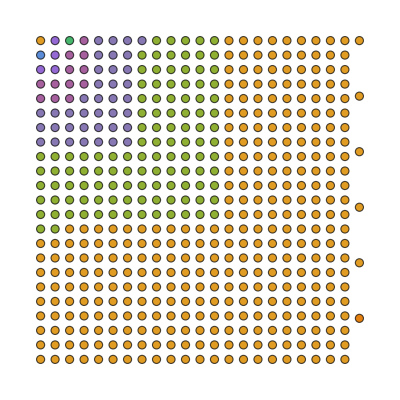

```mathematica
SetReplace[s345⟦66,1⟧,FromAnonymousRules[s345⟦66,2⟧],511]//
```

In conclusion, we mostly get rules of class 1, and a few extremely simple examples of class 2.

## Analysis of sizes [6, 8]

For larger sizes, we have to use some kind of automatic filtering algorithm, because otherwise the number of rules we will have to examine will go out of hand.

```mathematica
s678=Flatten[allSystems/@Range[6,8],1];
```

There are now many more rules in total

```mathematica
Length[s678]
```

193501

### Growth (number of edges)

One thing we can filter on is the total number of edges after 100 steps

```mathematica
DistributeDefinitions["SetReplace`"];
edgeCounts678=ParallelMap[Length[SetReplace[#⟦1⟧,FromAnonymousRules[#⟦2⟧],100,Method->"WolframLanguage"]]&,s678];
```

```mathematica
KeySort@Counts[edgeCounts678]
```

<|1→114467,2→41492,3→12846,4→4575,5→611,6→232,34→43,100→32,101→2704,102→3326,103→1830,104→496,105→64,201→4668,202→2068,203→496,204→64,301→2239,302→528,303→64,401→528,402→64,501→64|>

We can see most rules have either only a very small number of edges (≤6), or a large one (≥34). In other words, some rules yield growing systems, and some die out quite quickly

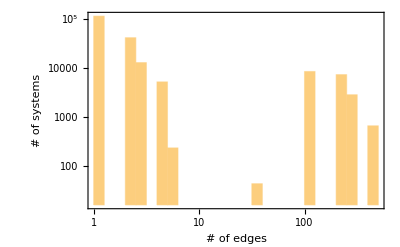

```mathematica
Histogram[edgeCounts678,]
```

We only care for rules that keep growing, so we can make a filtering function

```mathematica
ruleGrows[ruleIndex_]:=edgeCounts678⟦ruleIndex⟧≥7
```

### Connected components

The next thing we can examine is the number of connected components. If there are too many, that necessarily implies the system produces repetitive behavior, as there can be no interaction between components that are not connected to one another.

```mathematica
DistributeDefinitions["SetReplace`"];
componentCounts678=ParallelMap[Length@ConnectedComponents[Graph[UndirectedEdge@@@Flatten[Partition[#,2,1]&/@(SetReplace[#⟦1⟧,FromAnonymousRules[#⟦2⟧],100,Method->"WolframLanguage"]),1]]]&,s678];
```

```mathematica
KeySort@Counts[componentCounts678]
```

<|0→104873,1→68533,2→6953,3→1217,4→393,5→55,6→26,17→6,25→15,26→43,33→9,34→268,35→18,49→7,50→531,51→529,52→36,66→18,67→201,68→9,75→33,76→11,97→5,98→46,99→296,100→6397,101→1929,102→42,150→90,151→72,199→28,200→812|>

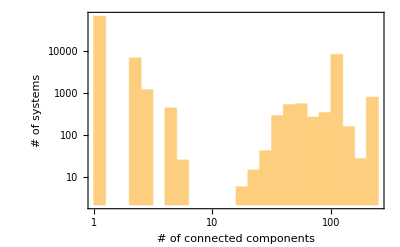

```mathematica
Histogram[componentCounts678,]
```

If we have as many connected components as rules, it either means the system’s behavior is repetitive, or that there exists a simpler system (that only keeps the largest component) that would produce a behavior similar to the largest component of the original system.

So, we will remove the systems that have 97 connected components or more

```mathematica
ruleMostlyConnected[ruleIndex_]:=componentCounts678⟦ruleIndex⟧≤96
```

### Single-vertex-input rules

Finally, if a rule’s input only contains a single single-vertex edge, we know this rule can not produce more complex than nested behavior. So, we will filter out those rules as well:

```mathematica
ruleNotSingleNested[ruleIndex_]:=s678⟦ruleIndex,2,1,1⟧≠{{1}}
```

### All remaining rules

The rule numbers that survive these filters are

```mathematica
interestingRules678=Select[ruleGrows[#]&&ruleMostlyConnected[#]&&ruleNotSingleNested[#]&]@Range@Length@s678;
```

```mathematica
Length[interestingRules678]
```

1207

This is actually possible (if somewhat monotonous) to examine by hand

```mathematica
Manipulate[Column[{interestingRules678⟦k⟧,s678⟦interestingRules678⟦k⟧⟧,HypergraphPlot[SetReplace[#⟦1⟧,FromAnonymousRules[#⟦2⟧],100,Method->"WolframLanguage"],ImageSize->500]}]&@s678⟦interestingRules678⟦k⟧⟧,{k,1,Length[interestingRules678],1},SaveDefinitions->True]
```

Some notable examples are

A rule that produces a tree by adding new edges to the ends of existing ones (class 2)

```mathematica
s678⟦107854⟧
```

{{{1,1}},{{{1,2}}→{{1,2},{2,3}}}}

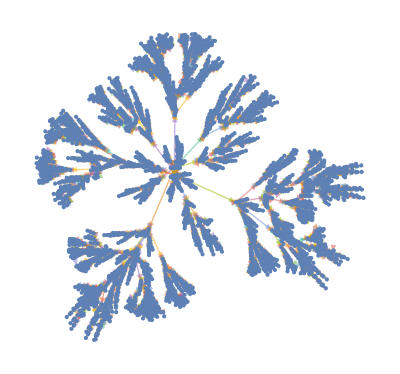

```mathematica
SetReplace[s678⟦107854,1⟧,FromAnonymousRules[s678⟦107854,2⟧],4000]//
```

A similar rule except it reverses the original edges (class 2)

```mathematica
s678⟦107861⟧
```

{{{1,1}},{{{1,2}}→{{1,3},{2,1}}}}

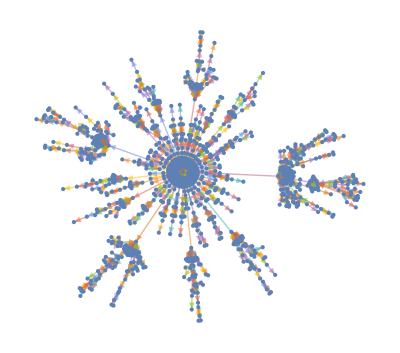

```mathematica
SetReplace[s678⟦107861,1⟧,FromAnonymousRules[s678⟦107861,2⟧],1000]//
```

A very simple rule that just makes a circle (class 1)

```mathematica
s678⟦107863⟧
```

{{{1,1}},{{{1,2}}→{{1,3},{2,3}}}}

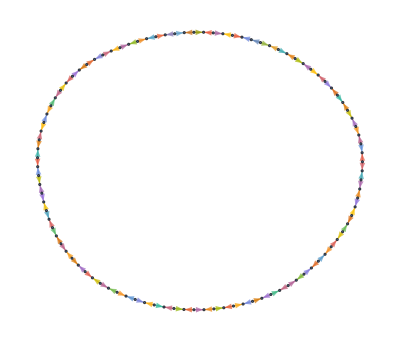

```mathematica
SetReplace[s678⟦107863,1⟧,FromAnonymousRules[s678⟦107863,2⟧],100]//
```

Here is another example of class 1

```mathematica
s678⟦117515⟧
```

{{{1,2}},{{{1,2}}→{{1,1},{2,1}}}}

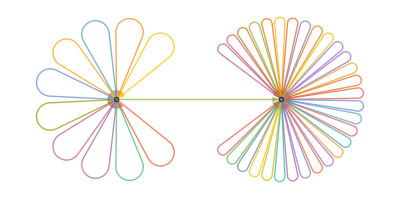

```mathematica
SetReplace[s678⟦117515,1⟧,FromAnonymousRules[s678⟦117515,2⟧],40]//
```

However, we still don’t find class 3 or 4 behavior.

## Issues and future work

### Rule application order

Rule considered here are not generally causally invariant, meaning that they will produce different networks if rules are applied in a different order.

That means there is ambiguity, because we can choose a different application order. In our case, the first rule always takes precedence, and it is applied to oldest edges first.

However, we can consider a different order, for instance, we can replace the newest edges first instead. That means we might have missed some potential complexity because we did not evaluate the system in the right order.

### Filtering

We only examined rules up to size 8, above that it becomes quite unmanageable to examine rules by hand. It will be useful to have automatic classification of rules into complexity classes.

### No class 3 or 4

We did not find any systems that produce class 3 or 4 behavior. We will need to consider larger rules. The simplest known example that still produces complexity is

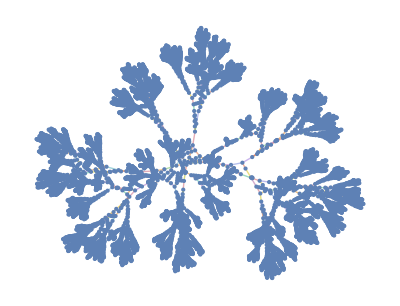

```mathematica
SetReplace[{{0,0},{0,0},{0,0}},FromAnonymousRules[{{0,1},{0,2},{0,3}}->{{1,6},{6,4},{6,5},{5,6},{6,3},{3,4},{5,2}}],5000]//
```

which is still size 26. So, the only thing we know is that class 3|4 behavior first appears in a system with a size between 9 and 26, and it is an open question which size exactly.

## Conclusion

We have examined Set Replace systems of up to size 8. We did find rules producing class 1 (repetitive) and 2 (nesting) behavior, but nothing of class 3 (pseudorandom) or 4 (complex).

We know class 3|4 behavior first appears in system sizes between 9 and 26, but it is an open question to pinpoint it to a specific size.